```mathematica
ν[m_][i_][T[i_,j_]]:=(-1)^j qi[m]^-1(
If[j>0,(-1)^(m-i)qi[i+j]T[i+1,j-1],0]+
If[i+j>m/2,(-1)^(m/2)qi[2i+j-m/2]T[i+1,j-2],0]+
If[i+j<m/2,(-1)^(m/2)qi[j+m/2]T[i+1,j],0]
)
```

```mathematica
ν[m_][i_][a_ t_T]:=a ν[m][i][t]
ν[m_][i_][X_Plus]:=ν[m][i]/@X
```

```mathematica
resμ[m_][i_,z_][T[i_,j_]]:=Sum[
1/(m-2i)(Sum[ζ[m-2i]^(-ℓ(j-jp))((-1)^i qi[m-i]/qi[m] ζ[m-2i]^-ℓ+(-1)^(m-i)qi[i]/qi[m] ζ[m-2i]^ℓ-z)^-1,{ℓ,0,m-2i-1}])T[i,jp]
,{jp,0,m-2i-1}]
```

```mathematica
resμ[m_][i_,z_][a_ t_T]:=a resμ[m][i,z][t]
resμ[m_][i_,z_][X_Plus]:=resμ[m][i,z]/@X
resμ[m_][i_,z_][X_Times]:=resμ[m][i,z][Expand[X]]
```

```mathematica
Clear[X]
X[m_,ω_][0]:=Sum[ω^-j T[0,j],{j,0,m-1}]
X[m_,ω_][i_]:=X[m,ω][i]=Collect[-resμ[m][i,ω][ν[m][i-1][X[m,ω][i-1]]],_T,Together]
```

```mathematica
Clear[ζ]
```

```mathematica
ζ/:ζ[n_]^m_/;m≥n:=ζ[n]^Mod[m,n]
```

```mathematica
ζ/:ζ[8]^(n_?EvenQ):=ⅈ^(n/2)
ζ/:ζ[8]^(n_?OddQ):=ⅈ^((n-1)/2)ζ[8]
```

```mathematica
ζ/:ζ[6]^(n_/;n≥3):=ζ[6]^Mod[n,3](-1)^Floor[n/3]
```

```mathematica
qi[k_]:=(q^k-q^-k)/(q-q^-1)
```

```mathematica
γ[j_]/;j>1:=γ[Mod[j,2]]
```

```mathematica
Clear[a]
a[m_][σ_,ω_]:=a[m][σ,ω]=Collect[X[m,ω][1]/.T[1,j_]:>σ^j γ[j+1],_γ,Together]
```

```mathematica
Clear[b]
b[n_][σ_,ω_]:=b[n][σ,ω]=∑_(j=0)^n (ω^-j+ω^(-j+n+1))((-1)^j(σ^j qi[2n+2-j]+σ^(j-2)qi[j])γ[j]+(-1)^(n+j+1)(σ^(j+1)qi[n+1-j]+σ^(j-1)qi[n+1+j])γ[j+1])
```

```mathematica
Clear[Z]
Z[n_,σ_,ω_]:=Z[n,σ,ω]=a[2n+2][σ,ω](q^(2n+2)+q^(-2n-2)-σ^2-σ^-2)+b[n][σ,ω]
```

Ok, we have everything set up.  Recall this abstractly only works for unshaded planar algebras with our current setup, so lets check the data for 2221.  Here n=3, and σ=1, e^(4 πi/3).  Lets check for all Tenth roots of unity ω:

```mathematica
Simplify[Together[Z[3,1,1]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

0

```mathematica
Simplify[Together[Z[3,1,Exp[2π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,1,Exp[4π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

0

```mathematica
Simplify[Together[Z[3,1,Exp[6π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

$Aborted

```mathematica
Simplify[Together[Z[3,1,Exp[8π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,1,Exp[10π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,1,Exp[12π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,1,Exp[14π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],1]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],Exp[2π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],Exp[4π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],Exp[6π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],Exp[8π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],Exp[10π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],Exp[12π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],Exp[14π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

Now lets see what happens when we plug in a ``wrong” value for σ.... (spoiler alert, it goes haywire!)

```mathematica
w=Simplify[Together[Z[3,Exp[2π ⅈ/3],1]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

0

```mathematica
(* What about sigma just of the wrong order? *)
w=Simplify[Together[Z[3,Exp[10π ⅈ/8],1]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]];
```

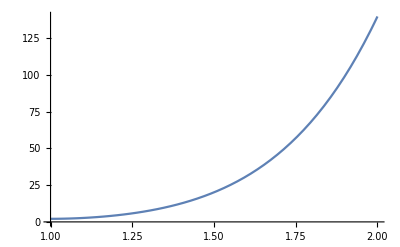

```mathematica
Plot[Abs[w],{q,1,2}]
```

This implies that our equation is non-trivial?  It looks like it could provide serious obstructions for the eigenvalues of generators?  Just to be sure we are not just getting lucky, lets check 4442 (also unshaded).  n=5, and σ=e^(2πi 8/10), which takes quite a long time...

```mathematica
v=Simplify[Together[Z[5,Exp[4π ⅈ/10],1]/._γ->1/.ζ[10]:>Exp[2π ⅈ/10]]]
```

-((8 (-1)^(1/5) (1-(-1)^(1/5)+(-1)^(2/5)-(-1)^(3/5)+(-1)^(4/5)) (-1+q)^10 (1+q)^8 (1+q^2+q^4+q^6+q^8+q^10)^10 (1+q^2+q^4+q^6+q^8+q^10+q^12+q^14+q^16+q^18+q^20)^4)/(5 q^11 (1+(-1)^(3/5) q+q^2+(-1)^(3/5) q^3+q^4+(-1)^(3/5) q^5+q^6+(-1)^(3/5) q^7+q^8+(-1)^(3/5) q^9+q^10+(-1)^(2/5) (-1+(-1)^(1/5)) q^11+q^12+(-1)^(3/5) q^13+q^14+(-1)^(3/5) q^15+q^16+(-1)^(3/5) q^17+q^18+(-1)^(3/5) q^19+q^20+(-1)^(3/5) q^21+q^22) (1+(-1)^(4/5) q+q^2+(-1)^(4/5) q^3+q^4+(-1)^(4/5) q^5+q^6+(-1)^(4/5) q^7+q^8+(-1)^(4/5) q^9+q^10+(-1)^(1/5) (-1+(-1)^(3/5)) q^11+q^12+(-1)^(4/5) q^13+q^14+(-1)^(4/5) q^15+q^16+(-1)^(4/5) q^17+q^18+(-1)^(4/5) q^19+q^20+(-1)^(4/5) q^21+q^22) ((-1)^(1/5)+q+(-1)^(1/5) q^2+q^3+(-1)^(1/5) q^4+q^5+(-1)^(1/5) q^6+q^7+(-1)^(1/5) q^8+q^9+(-1)^(1/5) q^10+(1+(-1)^(2/5)) q^11+(-1)^(1/5) q^12+q^13+(-1)^(1/5) q^14+q^15+(-1)^(1/5) q^16+q^17+(-1)^(1/5) q^18+q^19+(-1)^(1/5) q^20+q^21+(-1)^(1/5) q^22) ((-1)^(1/5)-(-1)^(2/5) q+(-1)^(1/5) q^2-(-1)^(2/5) q^3+(-1)^(1/5) q^4-(-1)^(2/5) q^5+(-1)^(1/5) q^6-(-1)^(2/5) q^7+(-1)^(1/5) q^8-(-1)^(2/5) q^9+(-1)^(1/5) q^10-(1+(-1)^(2/5)) q^11+(-1)^(1/5) q^12-(-1)^(2/5) q^13+(-1)^(1/5) q^14-(-1)^(2/5) q^15+(-1)^(1/5) q^16-(-1)^(2/5) q^17+(-1)^(1/5) q^18-(-1)^(2/5) q^19+(-1)^(1/5) q^20-(-1)^(2/5) q^21+(-1)^(1/5) q^22) ((-1)^(1/5)+(-1)^(2/5) q+(-1)^(1/5) q^2+(-1)^(2/5) q^3+(-1)^(1/5) q^4+(-1)^(2/5) q^5+(-1)^(1/5) q^6+(-1)^(2/5) q^7+(-1)^(1/5) q^8+(-1)^(2/5) q^9+(-1)^(1/5) q^10+(1+(-1)^(2/5)) q^11+(-1)^(1/5) q^12+(-1)^(2/5) q^13+(-1)^(1/5) q^14+(-1)^(2/5) q^15+(-1)^(1/5) q^16+(-1)^(2/5) q^17+(-1)^(1/5) q^18+(-1)^(2/5) q^19+(-1)^(1/5) q^20+(-1)^(2/5) q^21+(-1)^(1/5) q^22) ((-1)^(2/5)+q+(-1)^(2/5) q^2+q^3+(-1)^(2/5) q^4+q^5+(-1)^(2/5) q^6+q^7+(-1)^(2/5) q^8+q^9+(-1)^(2/5) q^10+(1+(-1)^(4/5)) q^11+(-1)^(2/5) q^12+q^13+(-1)^(2/5) q^14+q^15+(-1)^(2/5) q^16+q^17+(-1)^(2/5) q^18+q^19+(-1)^(2/5) q^20+q^21+(-1)^(2/5) q^22) ((-1)^(2/5)-(-1)^(4/5) q+(-1)^(2/5) q^2-(-1)^(4/5) q^3+(-1)^(2/5) q^4-(-1)^(4/5) q^5+(-1)^(2/5) q^6-(-1)^(4/5) q^7+(-1)^(2/5) q^8-(-1)^(4/5) q^9+(-1)^(2/5) q^10-(1+(-1)^(4/5)) q^11+(-1)^(2/5) q^12-(-1)^(4/5) q^13+(-1)^(2/5) q^14-(-1)^(4/5) q^15+(-1)^(2/5) q^16-(-1)^(4/5) q^17+(-1)^(2/5) q^18-(-1)^(4/5) q^19+(-1)^(2/5) q^20-(-1)^(4/5) q^21+(-1)^(2/5) q^22) ((-1)^(2/5)+(-1)^(4/5) q+(-1)^(2/5) q^2+(-1)^(4/5) q^3+(-1)^(2/5) q^4+(-1)^(4/5) q^5+(-1)^(2/5) q^6+(-1)^(4/5) q^7+(-1)^(2/5) q^8+(-1)^(4/5) q^9+(-1)^(2/5) q^10+(1+(-1)^(4/5)) q^11+(-1)^(2/5) q^12+(-1)^(4/5) q^13+(-1)^(2/5) q^14+(-1)^(4/5) q^15+(-1)^(2/5) q^16+(-1)^(4/5) q^17+(-1)^(2/5) q^18+(-1)^(4/5) q^19+(-1)^(2/5) q^20+(-1)^(4/5) q^21+(-1)^(2/5) q^22)))

Ok, lets find the value of q in 4442 and plug it in to the above expression....

```mathematica
Clear[qFromd]
qFromd[d_]:=qFromd[d]=RootReduce[Max[q/.Solve[q+q^(-1)==Sqrt[3+Sqrt[5]], q, Reals]]]
```

```mathematica
v/.q->qFromd[√(3+√5)]//RootReduce
```

0

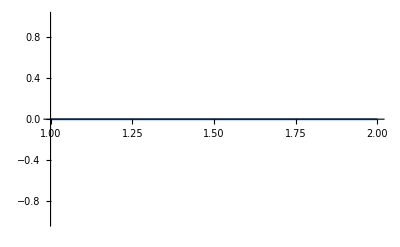

```mathematica
Plot[Abs[v],{q,1,2}]
```